#### 2. domača naloga

```mathematica
ClearAll["Global`*"]
```

### Naloga 1

Tako bo izgledala definicija daljice ...

```mathematica
Daljica[A_, B_];
```

Dolžina daljice.

```mathematica
Dolzina[Daljica[A_, B_]] := Norm[B - A]
```

Izračunajmo enačbo nosilke daljice. Za vsak slučaj počistimo simbola x in y.

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

Alternativno ...

```mathematica
EnacbaNosilke[Daljica[AA_, BB_]] := Module[{k, n, x0, y0},
k = 1/Apply[Divide,BB -AA];
{x0, y0} = AA;
n = n /.First[Solve[y0 == x0*k + n, n]];
y == k*x + n
]
```

Preverimo na primeru.

```mathematica
d = Daljica[{-1, 1}, {3, -1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

Izračunajmo sliko daljice.

```mathematica
SlikaDaljice[Daljica[A_, B_]] := Line[{A, B}]
```

```mathematica
SlikaDaljice[d]
```

Line[{{-1,1},{3,-1}}]

Narišimo daljico.

```mathematica
ClearAll[Narisi]
Narisi[d__Daljica] := Graphics[{Map[SlikaDaljice, List[d]]}, AspectRatio->Full, Axes-> True]
```

Daljica[{2,-3},{4,2}]

Daljica[{0,1},{3,1}]

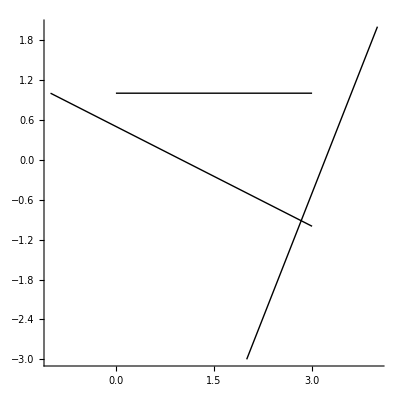

```mathematica
d2 = Daljica[{2,-3}, {4, 2}]
d3 = Daljica[{0,1}, {3, 1}]
Narisi[d, d2 , d3]
```

### Naloga 2

Izračunajmo presek daljic. Uporabimo vektorsko obliko premice r = r_o +s (r_B-r_A), kjer je smerni vektor definiran kar iz točk daljice A in B. Potem smo na daljici, če je parameter s na intervalu [0, 1].

```mathematica
ClearAll[PresekDaljic]
Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]] := Module[{r, s, resitev},
resitev =Solve[{AA + r(BB-AA) == CC + s(DD -CC), r ≥ 0, r ≤ 1, s≥0, s ≤ 1}, {r,s}];
If[Length[resitev] > 0,
AA + r*(BB -AA) /. First[resitev],
{}
]
]
```

```mathematica
Presek[d, d2]
```

{17/6,-11/12}

```mathematica
Presek[d, d3]
```

{}

### Naloga 3

Definirajmo primerek mnogokotnika na način, kot smo si "izmislili".

```mathematica
m1 = Mnogokotnik[{0,0}, {1,1}, {0, 3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Izračunajmo sliko. S funkcijo Append dodamo prvi element na konec seznama (v bistvu definiramo nov seznam za enim elementom več). Pozor : za definicijo parametra t smo uporabili dva podčrtaja. To pomeni, da namesto t__ pričakujemo "eno ali več stvari". Te “stvari” lahko za nadaljnje delo “stlačimo” najprej v seznam (funkcija List ali preprosto zavijemo okoli njih zavite oklepaje {...})

```mathematica
SlikaMnogokotnika[Mnogokotnik[t__]] := Line[Append[List[t], First[List[t]]]]
```

```mathematica
SlikaMnogokotnika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

Izris mnogokotnika.

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Map[SlikaMnogokotnika, List[m]]]
```

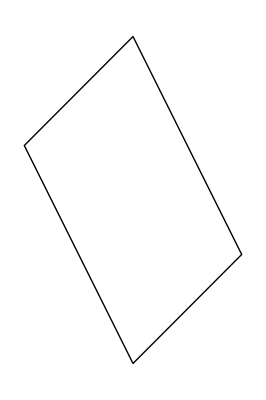

```mathematica
Narisi[m1]
```

Pravilni n - kotnik.

```mathematica
PravilniNKotnik[n_, r_] := Apply[Mnogokotnik, Table[{Cos[2*Pi*i/n], Sin[2*Pi*i/n]}, {i, 0, n-1}]]
```

Preizkusimo ...

```mathematica
p5 = PravilniNKotnik[5, 2]
```

Mnogokotnik[{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)}]

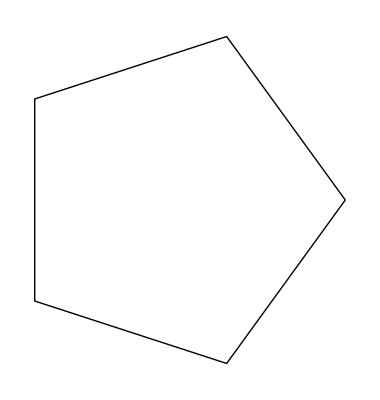

```mathematica
Narisi[p5]
```

Pa dodajmo še začetni kot ...

```mathematica
PravilniNKotnik[n_, r_, phi_] := Apply[Mnogokotnik, Table[{Cos[2*Pi*i/n + phi], Sin[2*Pi*i/n + phi]}, {i, 0, n-1}]]
```

In naredimo preizkus s pomočjo funkcije Manipulate, kjer spreminjamo začetni kot.

```mathematica
Manipulate[Narisi[PravilniNKotnik[5, 2, phi]], {phi, 0, Pi}]
```

Razbijmo mnogokotnik na daljice. Kaj naredita naslednji funkciji?

```mathematica
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Pretvorimo mnogokotnik v seznam točk in se malce poigrajmo z njim. Z Apply zamenjamo glavo "seznama" Mnogokotnik v novo glavo List.

```mathematica
tocke =Apply[List, m1]
```

{{0,0},{1,1},{0,3},{-1,2}}

Dodajmo v seznam prvo točko na koncu. V bistvu naredimo nov seznam, kjer se prva točka ponovi.

```mathematica
Append[tocke, First[tocke]]
```

Kaj naredi Partition na pare z zamikom 1?

```mathematica
Partition[Append[tocke, First[tocke]], 2, 1]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

```mathematica
A niso to slučajno ravno točke daljic (stranic)? Samo še Daljica moramo "mapniti čez" pa smo dobili rezultat... No ni čisto res. Ločiti moramo med našo definicijo daljice Daljica[AA, BB] in kaj dobimo, če "mapnemo" glavo Daljica, t.j. Daljica[{AA, BB}]. Zato si naredimo priročno funkcijo za pretvorbo.
```

```mathematica
Daljica[{AA_, BB_}] := Daljica[AA, BB]
Daljice[Mnogokotnik[t__]] := Map[Daljica, Partition[Append[List[t], First[List[t]]], 2, 1]]
```

Preverimo rezultat.

```mathematica
Daljice[p5]//N
```

{Daljica[{1.,0.},{0.309017,0.951057}],Daljica[{0.309017,0.951057},{-0.809017,0.587785}],Daljica[{-0.809017,0.587785},{-0.809017,-0.587785}],Daljica[{-0.809017,-0.587785},{0.309017,-0.951057}],Daljica[{0.309017,-0.951057},{1.,0.}]}

### Naloga 4

Oglejmo si primer, na katerem se bomo poigrali.

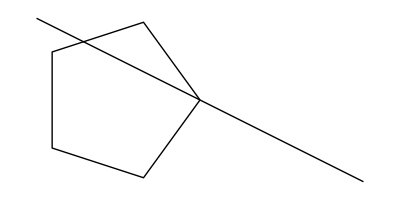

```mathematica
Graphics[{SlikaMnogokotnika[p5], SlikaDaljice[d]}]
```

Osnovna ideja je:
- Znamo že narediti presek dveh daljic (funkcija Presek zgoraj).
- Znamo tudi razbiti mnogokotnik na seznam daljic.
- Kar moramo še narediti, je poračunati presek dane daljice z vsako iz seznama. Ta je lahko neka točka ali pa prazna množica (seznam).
Če bi imeli funkcijo, ki izračuna presek izbrane daljice s poljubno drugo, bi to funkcijo enostavno “mapnili” čez seznam daljic mnogokotnika. Tako funkcijo lahko naredimo, če “zapečemo” en parameter.

```mathematica
d
```

Daljica[{-1,1},{3,-1}]

```mathematica
presekZD[d2_] := Presek[d, d2]
```

"Mapnimo" to funkcijo čez seznam daljic.

```mathematica
Map[presekZD, Daljice[p5]] //N
```

{{1.,0.},{-0.425073,0.712536},{},{},{1.,0.}}

Dobimo nekaj rešitev, ki celo izgledajo smiselno glede na sliko zgoraj ... Problem, je kar nam gredo na živce ponovitve presečišč (v vogalih) ter prazne rešitve. Zaželjene rešitve (ki niso prazne) dobimo s pomočjo funkcije Select. Ta glede na testno funkcijo izbere elemente iz seznama. Testne funkcije vrnejo True (je res) ali False (ni res). Napišimo testno funkcijo, ki preveri, ali je seznam neprazen.

```mathematica
jeNeprazen[l_List] := Length[l] > 0
```

```mathematica
jeNeprazen[{1,2}]
```

True

```mathematica
jeNeprazen[{}]
```

False

Preizkusimo ...

```mathematica
Select[Map[PresekZD, Daljice[p5]], jeNeprazen] //N
```

{{1.,0.},{-0.425073,0.712536},{1.,0.}}

Sedaj se moramo rešiti samo še dvojnikov. Tu nam pomaga funkcija, katere ime pove vse : DeleteDuplicates.

```mathematica
DeleteDuplicates[Select[Map[PresekZD, Daljice[p5]], jeNeprazen]] //N
```

{{1.,0.},{-0.425073,0.712536}}

Sedaj pa to vse zapakirajmo v funkcijo. Problem, ki ga imamo, da smo samo za ta namen posebej definirali dve pomožni funkciji, pri čemer je prva ( presekZD) še vezana na konkretno daljico, kar je za splošno rabo malce nepriročno - saj bi morali za vsako daljico definirati svojo funkcijo. To dejansko naredimo “sproti” v Module, kjer sta definiciji funkcij lokalni (vidni samo začasno v času izvajanja funkcije).

```mathematica
Presek[m_Mnogokotnik, d_Daljica] := Module[{presekZD, jeNeprazen},
presekZD[d2_] := Presek[d, d2];
jeNeprazen[l_List] := Length[l] > 0;
DeleteDuplicates[Select[Map[PresekZD, Daljice[p5]], jeNeprazen]]
]
```

Preizkusimo

```mathematica
Presek[p5, d]//N
```

{{1.,0.},{-0.425073,0.712536}}

Če želimo zadevo napisati malce bolj elegantno, lahko uporabimo anonimne funkcije. Namesto funkcij presekZD in jeNeprazen, definiramo anonimni funkciji:

```mathematica
Presek[d, #]&
Length[#]>0&
```

Presek[d,#1]&

Length[#1]>0&

In ju seveda takoj uporabimo ...

```mathematica
Presek[m_Mnogokotnik, d_Daljica] := DeleteDuplicates[Select[Map[Presek[d, #]&, Daljice[m]], Length[#]>0&]]
```

```mathematica
Presek[p5, d]//N
```

{{1.,0.},{-0.425073,0.712536}}

### Naloga 5

Poglejmo, kaj naredi funkcija VsiPari.

```mathematica
VsiPari[f_, sez1_, sez2_] :=Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2, 3}, {a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

Kot že ime pravi, izračuna funkcijo na vseh kombinacijah, ki določajo pare. Če želijo izračunat preseke dveh mnogokotnikov, enostavno naredimo tole:
- izračunamo seznama daljic obeh pravokotnikov,
- poiščemo presek vsake daljice iz prvega pravokotnika z vsako iz drugega.
Poglejmo primer:

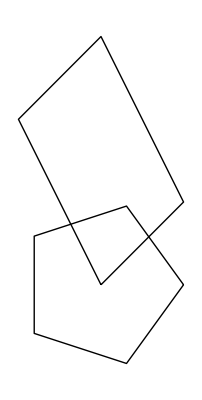

```mathematica
Narisi[m1, p5]
```

Uporabimo funkcijo Presek na vsakem paru (namest f v primeru zgoraj).

```mathematica
VsiPari[Presek, Daljice[m1], Daljice[p5]] //N
```

{{0.579192,0.579192},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{-0.365884,0.731768},{},{},{}}

Dobimo ravno dve presečišči pa množico praznih rešitev. Zavedamo, se da bi se na ogliščih presečišča ponavaljala. Zato uporabimo isti prijem kot zgoraj (Select, DeleteDuplicates).

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik] := DeleteDuplicates[Select[VsiPari[Presek, Daljice[m1], Daljice[m2]], Length[#]>0&]]
```

```mathematica
Presek[m1, p5]//N
```

{{0.579192,0.579192},{-0.365884,0.731768}}

Kaj naredi funkcija Outer?

```mathematica
Outer[f, {1, 2, 3}, {a, b}]
```

{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

```mathematica
Outer[f, {1, 2, 3}, {a, b}, {A, B, C}]
```

{{{f[1,a,A],f[1,a,B],f[1,a,C]},{f[1,b,A],f[1,b,B],f[1,b,C]}},{{f[2,a,A],f[2,a,B],f[2,a,C]},{f[2,b,A],f[2,b,B],f[2,b,C]}},{{f[3,a,A],f[3,a,B],f[3,a,C]},{f[3,b,A],f[3,b,B],f[3,b,C]}}}

Fukcija Outer vrne vse možne kombinacije elementov seznamov.

Kaj naredi funkcija Flatten?

```mathematica
Flatten[{1, {2}}]
```

{1,2}

```mathematica
Flatten[{1, {2, 4}}]
```

{1,2,4}

Fukcija Flatten je funkcija nasprotna gnezdenju. Torej iz gnezdenih seznamov potegne ven elemente in jih zloži v en seznam.

#### Naloga iz Linearne algebre.

Izbrala sem si nalogo številka 3.6 iz tretje domače naloge.

```mathematica
a = {a1, a2, a3};
b = {b1, b2, b3};
c = {c1, c2, c3};
d = Simplify[Dot[Cross[a+b, b+c],c+a]];
e = Simplify[2*Dot[Cross[a,b], c]];
d==e
```

True

```mathematica
SetOptions[EvaluationNotebook[],Background-> Lighter[Lighter[Lighter[Magenta]]] ]
```